```mathematica
(*number 1a*)
Subscript[q, 0]=10^-4;
Subscript[q, 1]=10^-1;
p=0.9;
Ph0=p;
Ph1=1-p;
n=1+Log[(Ph0 Subscript[q, 0])/(Ph1 Subscript[q, 1])]/Log[(1-Subscript[q, 1])/(1-Subscript[q, 0])]
(*number 1b*)
pfa=Sum[(1-Subscript[q, 0])^(N-1)(Subscript[q, 0]),{N,1,45}]//N
pmd=1-Sum[(1-Subscript[q, 1])^(N-1)(Subscript[q, 1]),{N,1,45}]//N
p pfa + (1-p)pmd
```

45.7512

0.00449011

0.00872796

0.0049139

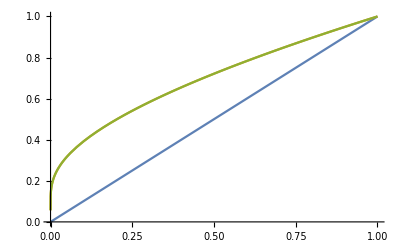

```mathematica
(*number 4*)
fvθx[θ_,x_]:=1/(θ Abs[Log[x]]);
fθx[x_] := fvθx[θ,x];
exp[x_]:=∫_x^1 θ fθx[x]ⅆθ;
Plot[{x,exp[x],∫_x^1 1/Abs[Log[x]] ⅆθ},{x,0,1}]
```

```mathematica
Table[fvθx[θ,.5],{θ,.5,1,.1}]
```

{2.88539,2.40449,2.06099,1.80337,1.60299,1.4427}

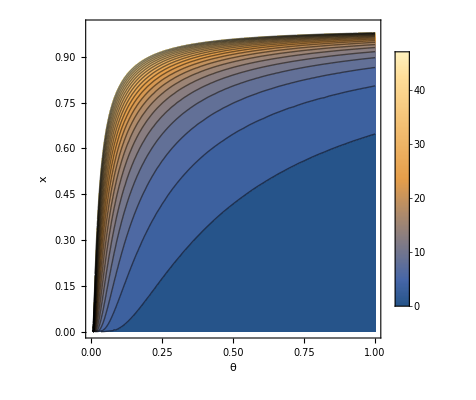

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ConditionalExpression[-Log[x]/Abs[Log[x]]==1,((Re[x/(1-x)]≥0&&x/(-1+x)≠0)||x/(1-x)∉Reals||Re[x/(1-x)]<-1)&&(x∉Reals||Re[x]>1||0<Re[x]<1)],x]

```mathematica
ContourPlot[fvθx[θ,x],{θ,0,1},{x,0,1},PlotLegends->Automatic,Contours->20,FrameLabel->Automatic]
Solve[Integrate[fvθx[θ,x],{θ,x,1}]==1,x]
```

```mathematica
Simplify[(1/2)+(1/6-1/8)/(7/144)(x-1/4)]
```

2/7 (1+3 x)

```mathematica
flow[θ_,x_]:=1/(11-x);
fmid[θ_,x_]:=1/2;
fhigh[θ_,x_]:=1/(x-3);
explow[x_]:=∫_4^5 θ flow[θ,x]ⅆθ
expmid[x_]:=∫_6^8 θ/2 ⅆθ
exphigh[x_]:=∫_9^10 θ fhigh[θ,x]ⅆθ
explow[x]
expmid[x]
exphigh[x]
Simplify[explow[x] + expmid[x] + exphigh[x]]
```

9/(2 (11-x))

7

19/(2 (-3+x))

7+9/(22-2 x)+19/(2 (-3+x))

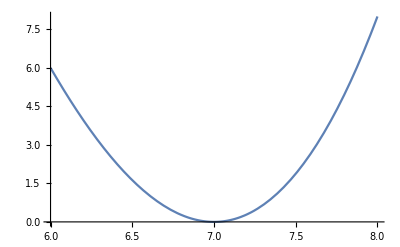

```mathematica
Plot[∫_4^6 x/2(x-7)^2ⅆθ,{x,6,8}]
```

```mathematica
n=500;
p=0.52;
μx = p;
σx=√(p(1-p));
μ=n μx;
σ=√(n^2 σx^2);
v = σ^2;
lowlim=μ-1.96 √(v/n)
uplim=μ+1.96 √(v/n)
```

238.104

281.896

```mathematica
n=500;
p=0.05;
μx = p;
σx=√(p(1-p));
μ=n μx;
σ=√(n^2 σx^2);
v = σ^2;
lowlim=μ-1.96 √(v/n)
uplim=μ+1.96 √(v/n)
```

15.4481

34.5519